```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/~$Книга1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1=makeDataset[raw⟦12⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"t"->(#t&),"dt"-> (Around[#dt, #ddt] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[Normal@dataset1[All,{"t","dt"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+1009.01 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 1009.01 | 8.50904 | 118.581 | 7.99823×10^-13

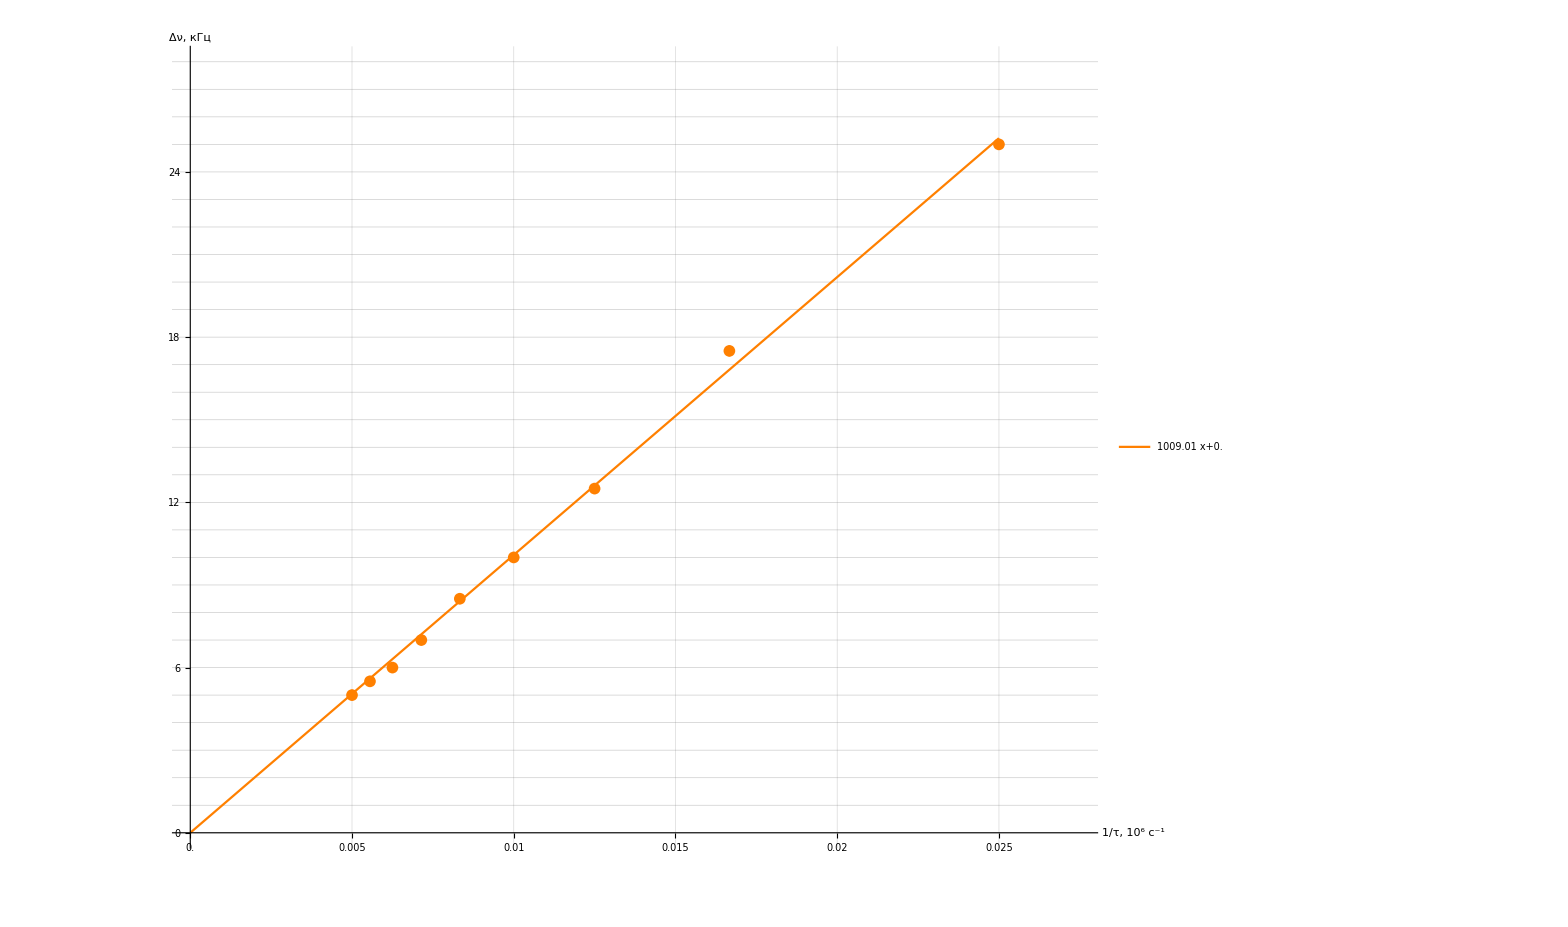

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
Ticks-> {Range[0,0.03,0.005],Range[0,1300,2]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["1/τ, 10^6 c^-1",Large],Style["Δν, кГц",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,0.0275},{0,28}},

GridLines->{Range[-0.1,2,0.001], Range[0,30,1]},
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{line1@x},
{x,0, 0.025},
PlotLegends->Placed[
LineLegend[
{Normal@line1},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
],
PlotStyle->Orange
]
]
```

```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/~$Книга1.xlsx}

```mathematica
importfile=files⟦2⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"nu"->(#nu&),"Ua"-> (Around[#Ua, #dU] &)|>]
```

Dataset[<>]

```mathematica
sin1 =NonlinearModelFit[Normal@dataset1[All,{"nu","Ua"}/*Values],Sin[a*x]/(b*x),{a,b},x]
```

FittedModel[(0.411674 Sin[0.159837 x])/x]

```mathematica
sin1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.159837 | 0.00118883 | 134.449 | 1.67109×10^-52
b | 2.42911 | 0.0274071 | 88.6306 | 1.19694×10^-45

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"nu"->(#nu&),"Ua"-> (Around[#Ua, #dU] &)|>]
```

Dataset[<>]

```mathematica
sin2 =NonlinearModelFit[Normal@dataset2[All,{"nu","Ua"}/*Values],Sin[a*x]/(b*x),{a,b},x]
```

FittedModel[(0.436437 Sin[0.314018 x])/x]

```mathematica
sin2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.314018 | 0.000565294 | 555.494 | 6.70283×10^-76
b | 2.29128 | 0.00881751 | 259.856 | 2.29464×10^-63

## График

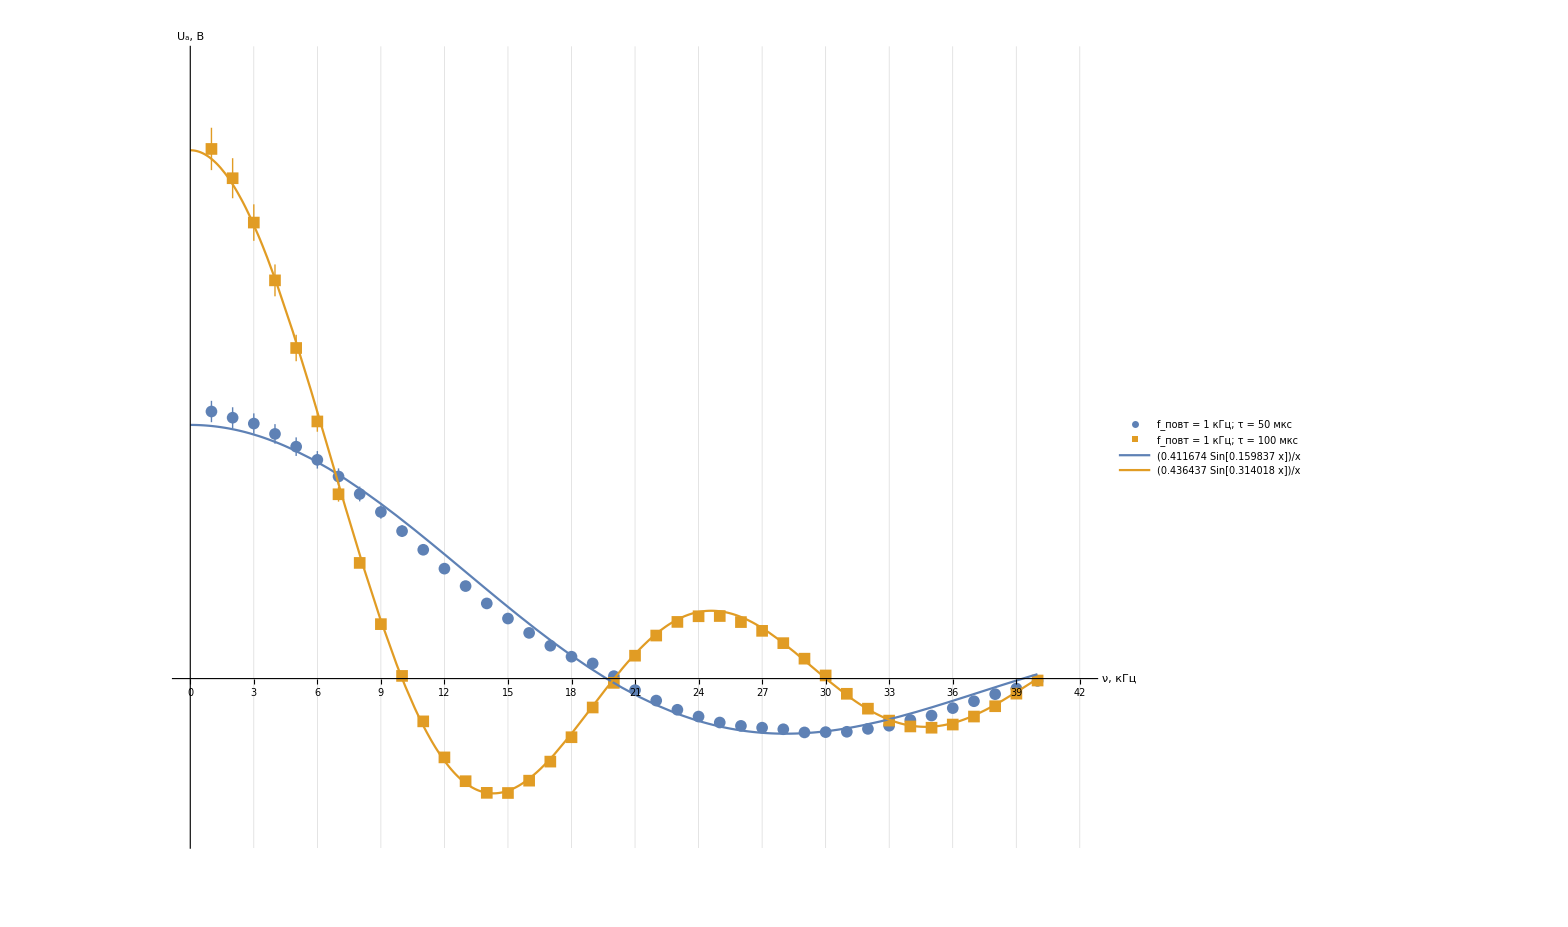

```mathematica
Show[
ListPlot[
{dataset1WithErrs,dataset2WithErrs},
Ticks-> {Range[0,50,1],Range[-20,3,0.01]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["ν, кГц",Large],Style["U_a, B",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,42},{-0.04,0.16}},

(*Filling->Axis,
FillingStyle->Thick,*)
GridLines->{Range[-0.1,50,0.5], Range[-20,30,0.005]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"f_(:043f:043e:0432:0442) = 1 кГц; τ = 50 мкс","f_(:043f:043e:0432:0442) = 1 кГц; τ = 100 мкс"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.4],Scaled[0.55]}
]
],
Plot[
{sin1@x,sin2@x},
{x,0, 40},
PlotLegends->Placed[
LineLegend[
{Normal@sin1,Normal@sin2},
LegendFunction->Framed,
LabelStyle->25
],
{Scaled[0.7],Scaled[0.75]}
]
]
]
```

## Другой очень информативный график

```mathematica
line1 =LinearModelFit[{{0.5,0.5},{1,1},{2,2},{3,3},{4,4},{5,5}},{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+1. x]

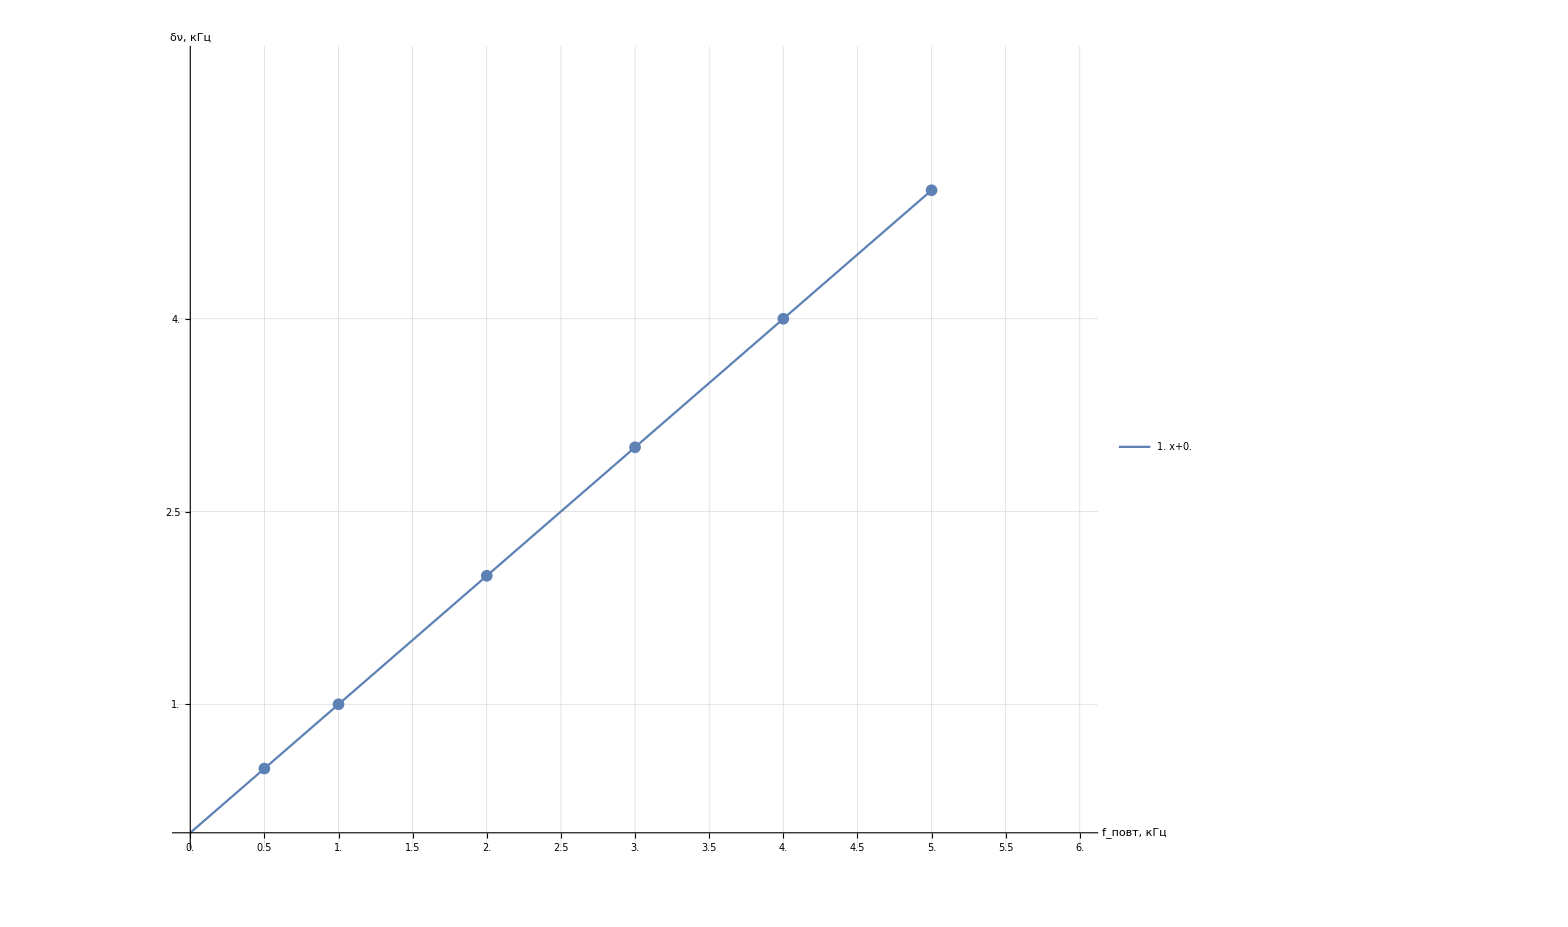

```mathematica
Show[
ListPlot[
{{0.5,0.5},{1,1},{2,2},{3,3},{4,4},{5,5}},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["f_(:043f:043e:0432:0442), кГц",Large],Style["δν, кГц",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,6},{0,6}},

(*Filling->Axis,
FillingStyle->0.25,*)

Ticks-> {Range[0,10,0.5],Range[-20,10,0.5]},
GridLines->{Range[0,10,0.2], Range[-20,10,0.2]},

LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"f_(:043f:043e:0432:0442) = 1 кГц; τ = 50 мкс","f_(:043f:043e:0432:0442) = 1 кГц; τ = 100 мкс"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.4],Scaled[0.55]}
]
],
Plot[
{line1@x},
{x,0, 5},
PlotLegends->Placed[
LineLegend[
{Normal@line1},
LegendFunction->Framed,
LabelStyle->25
],
{Scaled[0.34],Scaled[0.75]}
]
]
]
```

## Clear

```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/~$Книга1.xlsx}

```mathematica
importfile=files⟦2⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs,sin1,sin2,line1,line9]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦11⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"nu"->(#nu&),"Ua"-> (Around[#Ua, #dUa] &)|>]
```

Dataset[<>]

```mathematica
sin1 =NonlinearModelFit[Normal@dataset1[All,{"nu","Ua"}/*Values],a*Sin[b*x-30*b]/(b*x-30*b),{a,b},x]
```

FittedModel[-(3.08057 Sin[9.32553-0.310851 x])/(-9.32553+0.310851 x)]

```mathematica
sin1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.08057 | 0.0421599 | 73.0687 | 1.3017×10^-41
b | 0.310851 | 0.00278049 | 111.797 | 2.04906×10^-48

## Dataset 2

```mathematica
dataset2=makeDataset[raw⟦12⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"nu"->(#nu&),"Ua"-> (Around[#Ua, #dUa] &)|>]
```

Dataset[<>]

```mathematica
sin2 =NonlinearModelFit[Normal@dataset2[All,{"nu","Ua"}/*Values],a*Sin[b*x-30*b]/(b*x-30*b),{a,b},x]
```

FittedModel[-(6.21525 Sin[9.33074-0.311025 x])/(-9.33074+0.311025 x)]

```mathematica
sin2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 6.21525 | 0.149306 | 41.6276 | 1.49805×10^-18
b | 0.311025 | 0.00458914 | 67.774 | 3.96416×10^-22

## Грфик

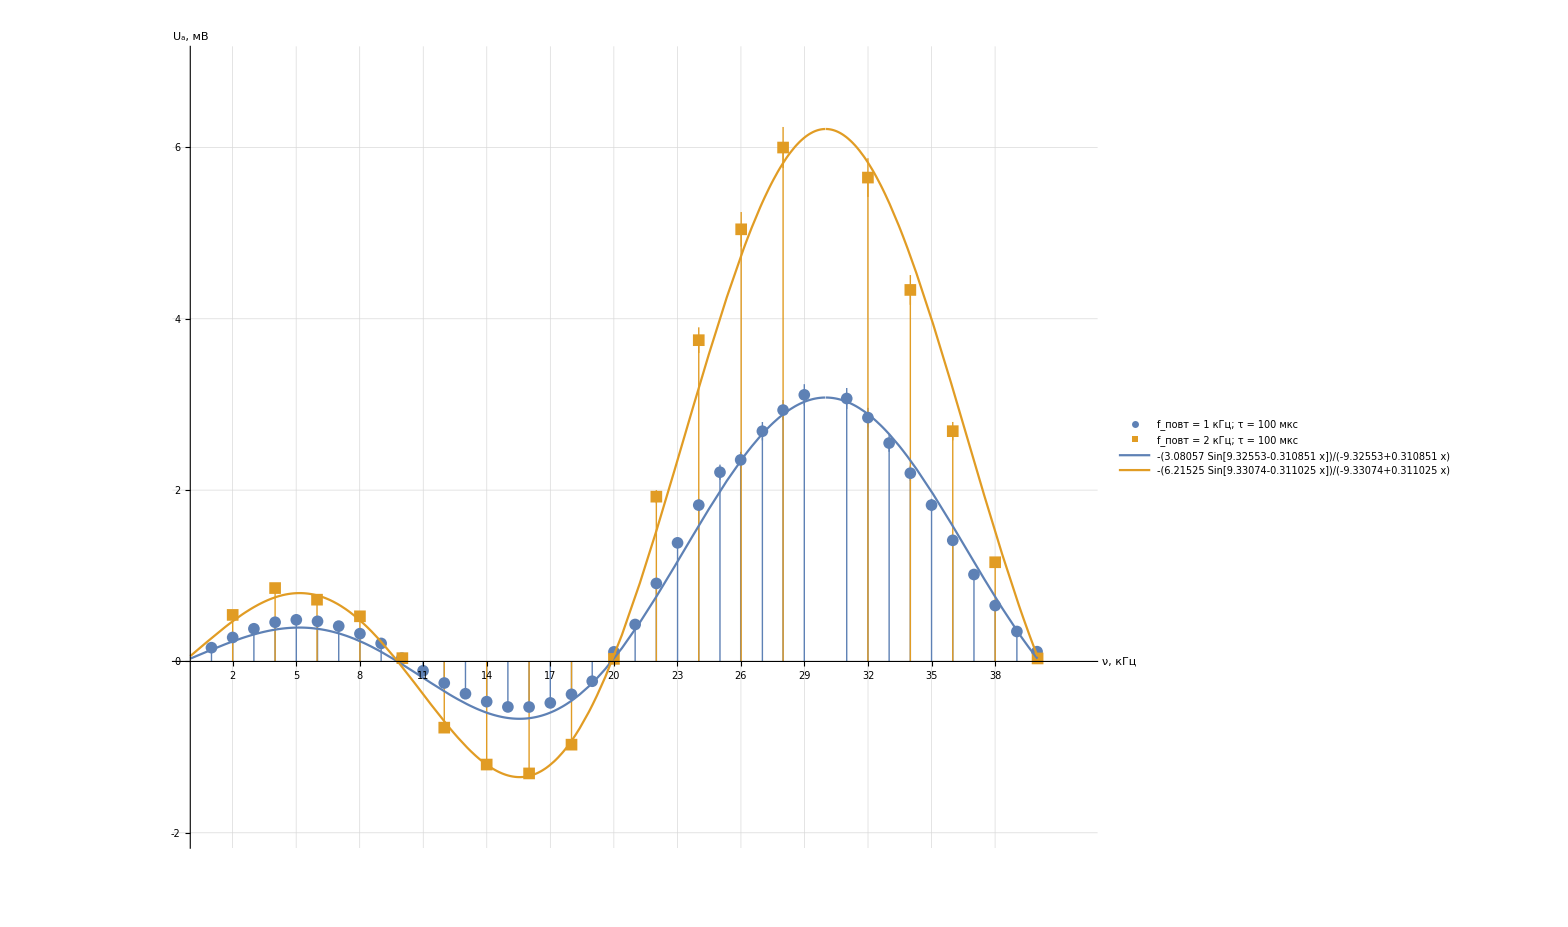

```mathematica
Show[
ListPlot[
{dataset1WithErrs,dataset2WithErrs},
Ticks-> {Range[-10,50,1],Range[-20,20,1]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["ν, кГц",Large],Style["U_a, мB",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,42},{-2,7}},

Filling->Axis,
FillingStyle->Thick,
GridLines->{Range[-0.1,50,0.5], Range[-20,30,0.25]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"f_(:043f:043e:0432:0442) = 1 кГц; τ = 100 мкс","f_(:043f:043e:0432:0442) = 2 кГц; τ = 100 мкс"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.33],Scaled[0.55]}
]
],
Plot[
{sin1@x,sin2@x},
{x,0, 40},
PlotLegends->Placed[
LineLegend[
{Normal@sin1,Normal@sin2},
LegendFunction->Framed,
LabelStyle->25
],
{Scaled[0.3],Scaled[0.75]}
]
](*,
Plot[
{Sin[0.3*x],2*Sin[0.3x]},
{x,0,20}
]*)
]
```

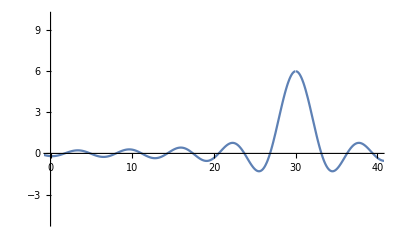

```mathematica
Plot[6*Sin[30-x]/(30-x),{x,-10,100},PlotRange->{{0,40},{-5,10}}]
```

## Clear

```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/~$Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/~$Книга2.xlsx}

```mathematica
importfile=files⟦2⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/361/Книга2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs,sin1,sin2,line1,line9]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦14⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"m"->(Around[#m,#dm]&),"a"-> (Around[#a, #da] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[Normal@dataset1[All,{"m","a"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.504446 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.504446 | 0.00761616 | 66.2336 | 7.96662×10^-10

## Грфик

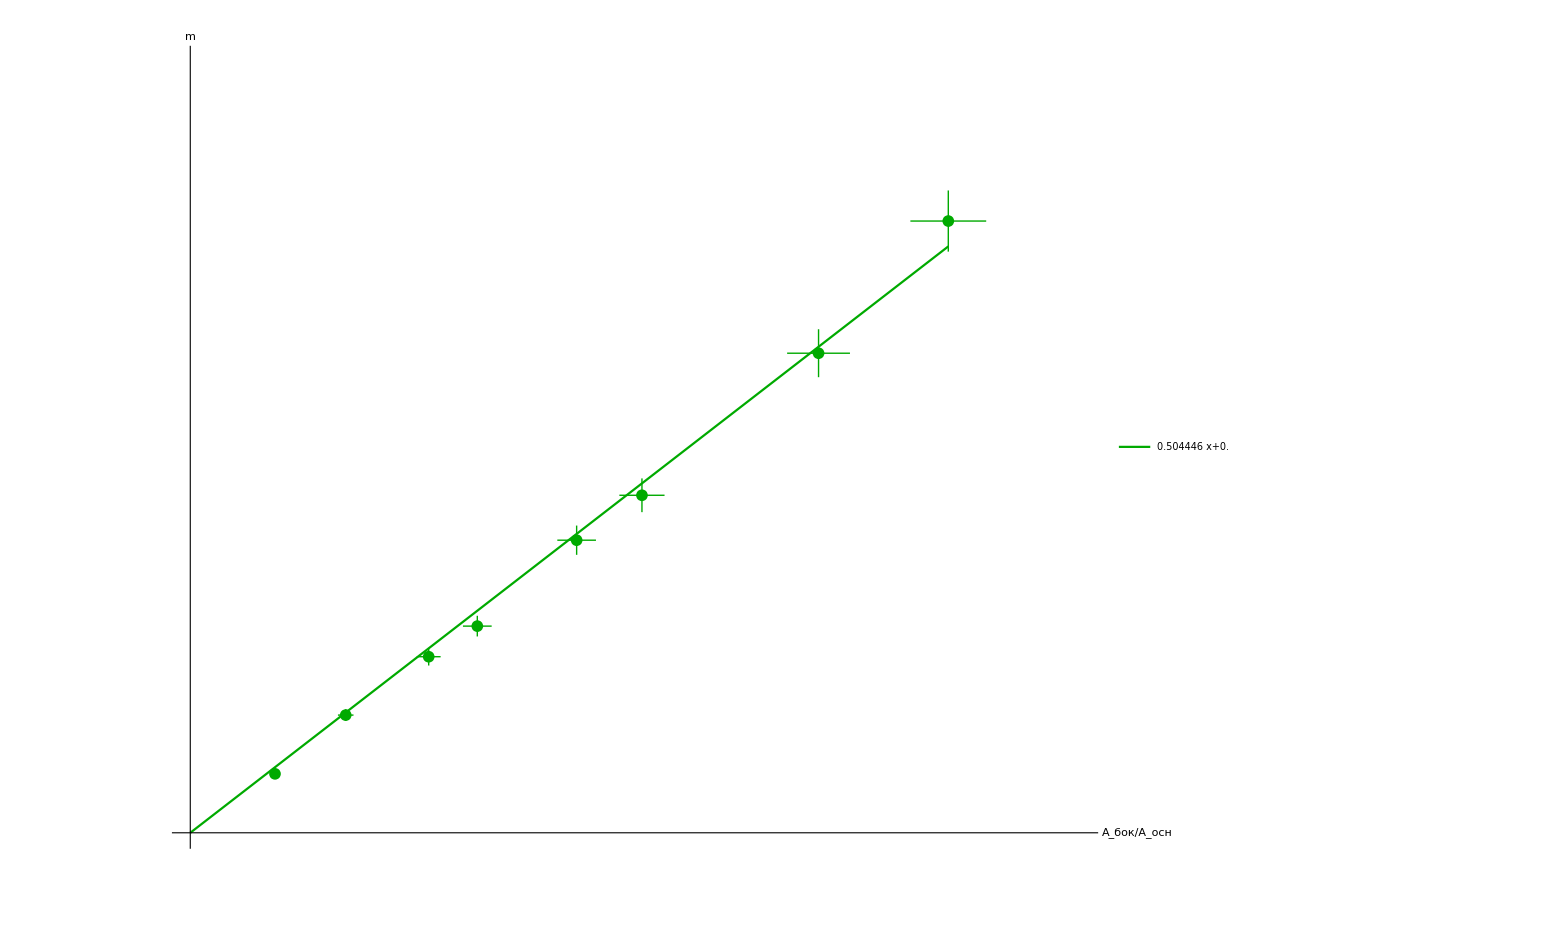

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
Ticks-> {Range[-10,50,0.1],Range[-20,20,0.1]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["A_(:0431:043e:043a)/A_(:043e:0441:043d)",Large],Style["m",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,1.15},{0,0.65}},

GridLines->{Range[-0.1,50,0.02], Range[-20,30,0.02]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"f_(:043f:043e:0432:0442) = 1 кГц; τ = 100 мкс","f_(:043f:043e:0432:0442) = 2 кГц; τ = 100 мкс"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.33],Scaled[0.55]}
],
PlotStyle->Darker@Green
],
Plot[
{line1@x},
{x,0, 0.98},
PlotLegends->Placed[
LineLegend[
{Normal@line1},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
],
PlotStyle->Darker@Green
]
]
```

```mathematica
Manipulate[Plot[1+m*Cos[a*x],{x,-10,10}],{m,0,1},{a,0,2}]
```